```mathematica
seg[{a_,b_,n_}]:=Graphics[Line[{{a,n},{b,n}}]];segs[list_]:=Show@@(seg/@Flatten/@Transpose[{list,Range[Length@list]/10}])
```

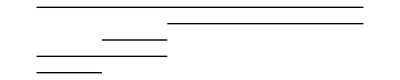

```mathematica
list={{2,3},{2,4},{3,4},{4,7},{2,7}};
segs[list]
```

```mathematica
??Show
```

Show[graphics,options] shows graphics with the specified options added. 
Show[g_1,g_2,…] shows several graphics combined.

Attributes[Show]={Protected,ReadProtected}

```mathematica
Transpose[{list,Range[Length@list]/10}]
```

{{{2,3},1/10},{{2,4},1/5},{{3,4},3/10},{{4,7},2/5},{{2,7},1/2}}

```mathematica
Flatten/@Transpose[{list,Range[Length@list]/10}]
```

{{2,3,1/10},{2,4,1/5},{3,4,3/10},{4,7,2/5},{2,7,1/2}}

{{1,5},{2,5},{3,5},{4,4},{4,5},{5,2},{5,3},{5,4},{5,5}}

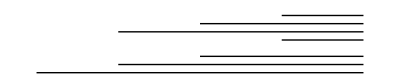

```mathematica
list1={{1,5},{2,5},{3,5},{4,4},{4,5},{5,2},{5,3},{5,4},{5,5}}
segs[list1]
```